```mathematica
n := 5
```

```mathematica
n
```

5

```mathematica
n := 100
```

```mathematica
m = 20
```

20

```mathematica
m
```

20

```mathematica
n
```

100

```mathematica
f = 0.1
```

0.1

```mathematica
DiscretePlot[Binomial[n, w] * (1/2 + 1/2 * (1 -2*0.01)^w)^m, {w, 1, n}]
```

-Graphics-

```mathematica
DiscretePlot[Binomial[n, w] , {w, 1, n}]
```

-Graphics-

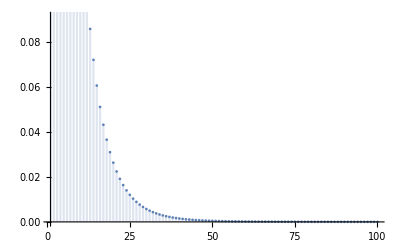

```mathematica
DiscretePlot[(1/2 + 1/2 * (1 -2*0.01)^w)^m, {w, 1, n}]
```

```mathematica
Plot[Sum[Binomial[n, w] * (1/2 + 1/2 * (1 -2*f)^w)^m, {w, 1, n}], {f, 0.02, 0.2}]
```

-Graphics-